```mathematica
f[n_]:= (2/l)^(1/2) Sin[n Pi x / l]
phi:=(1/l)^1/2 (1/4 - (x/l - 1/2)^2)
```

```mathematica
c[n_]:=Integrate[f[n] phi,{x,0,l}]
```

```mathematica
c[1]
```

(2 √2 √(1/l))/π^3

```mathematica
c[2]
```

0

```mathematica
c[3]
```

(2 √2 √(1/l))/(27 π^3)

```mathematica
c[4]
```

0

```mathematica
l := l
h:=h
```

```mathematica
sumF[n_]:= Sum[c[i]f[i],{i,1,n}]
```

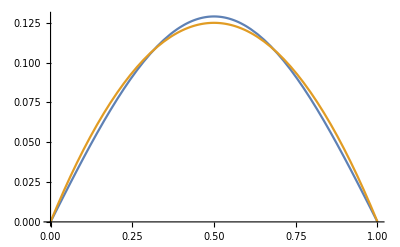

```mathematica
Plot[{Evaluate[sumF[2]],phi},{x,0,1}]
```

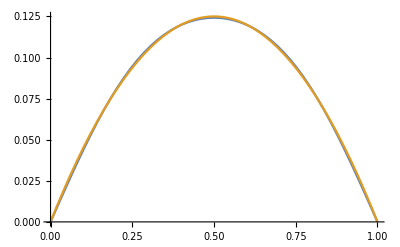

```mathematica
Plot[{Evaluate[sumF[4]],phi},{x,0,1}]
```

```mathematica
c[n]
```

-(-2+2 Cos[n π]+n π Sin[n π])/(√2 n^3 π^3)

```mathematica
|
```

```mathematica
Integrate[f[n] phi,x]
```

((1/l)^(5/2) ((-2 l^2-l n^2 π^2 x+n^2 π^2 x^2) Cos[(n π x)/l]+l n π (l-2 x) Sin[(n π x)/l]))/(√2 n^3 π^3)

```mathematica
(s Sin[n π x])/(4 √2)-(s (-1/2+x)^2 Sin[n π x])/(√2)
```

(s Sin[n π x])/(4 √2)-(s (-1/2+x)^2 Sin[n π x])/(√2)

```mathematica
Evaluate[((((1/l)^(5/2) ((-2 l^2-l n^2 π^2 x+n^2 π^2 x^2) Cos[(n π x)/l]+l n π (l-2 x) Sin[(n π x)/l]))/(√2 n^3 π^3))/. x->l) - ((((1/l)^(5/2) ((-2 l^2-l n^2 π^2 x+n^2 π^2 x^2) Cos[(n π x)/l]+l n π (l-2 x) Sin[(n π x)/l]))/(√2 n^3 π^3))/.x->0)]
```

(√2 √(1/l))/(n^3 π^3)+((1/l)^(5/2) (-2 l^2 Cos[n π]-l^2 n π Sin[n π]))/(√2 n^3 π^3)

```mathematica
(√2 √(1/l))/(n^3 π^3)+((1/l)^(5/2) (-2 l^2 Cos[n π]-l^2 n π Sin[n π]))/(√2 n^3 π^3)/. n-> 4
```

0